```mathematica
1.naloga
```

```mathematica
v0={10,3};
GG=9.81;
H=10;
a={0,-GG};
x0={0,H};
```

Formule iz fizike, nam povedo naslednje :
v(t) = v_0 + at
x(t) = x_0 + v_0 t + at^2/2

```mathematica
v[t_]:={v0[[1]],v0[[2]]-GG*t}
v[t_]:=v0 + a*t
X[t_]:=x0 + v0*t + (a*t^2)/2
```

```mathematica
SlikaTocke[t_]:={PointSize[0.03],Point[X[t]]};
Graphics[SlikaTocke[1]]
```

-Graphics-

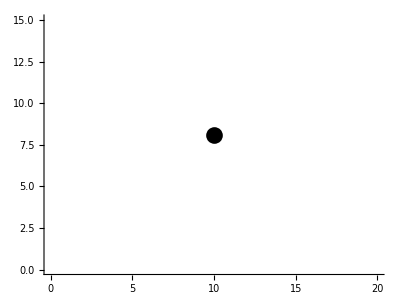

```mathematica
Graphics[SlikaTocke[1],Axes->True,PlotRange->{{0,20},{0,15}}]
```

```mathematica
Manipulate[Graphics[SlikaTocke[t],Axes->True,PlotRange->{{0,20},{0,15}}],{t,0,3}]
```

```mathematica
Manipulate[Graphics[{SlikaTocke[t],Arrow[{{1,1},{2,2}}]},Axes->True,PlotRange->{{0,20},{0,15}}],{t,0,3}]
```

```mathematica
SlikaTocke[t_] := {PointSize[0.02], Point[X[t]]}
Manipulate[Graphics[{SlikaTocke[t],Arrow[{X[t], X[t]+v[t]}]}, Axes->True, PlotRange->{ {-1, domet +3},{-1, NajvišjeTočka + 3}}, AspectRatio-> Automatic],{t, 0, časLeta}]
```

```mathematica
SlikaVektorja[t_]:=Arrow[{X[t], X[t]-v[t]}]
X[t][[2]] == 0
```

10+3 t-4.905 t^2==0

```mathematica
dolzinaHitrosti = (v0[[1]]^2+v0[[2]]^2)^(1/2)
sinkot =v0[[2]]/ dolzinaHitrosti //N
NajvišjeTočka = dolzinaHitrosti^2* sinkot^2 / (2*GG)+ H
```

√109

0.287348

10.4587

```mathematica
časLetaDonajvišjeTočke = 2*dolzinaHitrosti*sinkot/(GG *2)
domet  =dolzinaHitrosti^2 *Sin[2*ArcSin[sinkot]]/GG + H
```

0.30581

16.1162

```mathematica
časLeta= časLetaDonajvišjeTočke * 2 + (2*H/GG) ^(1/2)
```

2.03946

```mathematica
2.naloga
```

```mathematica
Slika[Ravnina[n_, v_]] := Hyperplane[n, v]
Format[r_Ravnina] := Graphics3D[Slika[r]]
Normala[Ravnina[n_, v_]] := n
Tocka[Ravnina[n_, v_]] := v
rx = Ravnina[{1, 0, 0}, {0, 0, 0}];
ry = Ravnina[{0, 1, 0}, {0, 0, 0}];
rz = Ravnina[{0, 0, 1}, {0, 0, 0}];
r111 = Ravnina[{-1, -1, -1},{1, 1, 1}]
ravnine = {rx, ry, rz, r111}
```

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SlikaNormale[Ravnina[n_, v_]] := Arrow[{v, v + n}]
slikeRavnin = Map[Slika, ravnine];
slikeNormal = Map[SlikaNormale, ravnine];
Graphics3D[{slikeRavnin, slikeNormal}, PlotRange->{{-1, 4}, {-1, 4},{-1, 4}}]
```

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_,v_]]:= Arrow[{ v + n, v}]
Graphics3D[{Slika[r111],SlikaNormale[r111]}]
```

-Graphics3D-

```mathematica
Enacba[Ravnina[n_, v_]]:=Module[{x, y, z,d},
d =n[[1]] v[[1]] + n[[2]] v[[2]] + n[[3]] v[[3]];
n[[1]] x + n[[2]] y+ n[[3]] z = d]
```

```mathematica
ravnine = {r111, rx};
obeSliki[r_Ravnina] := {Slika[r],SlikaNormale[r]}
Graphics3D[Map[obeSliki, ravnine]]
```

-Graphics3D-

```mathematica
Graphics3D[Map[{Slika[#],SlikaNormale[#]}&, ravnine]]
```

-Graphics3D-

```mathematica
EnacbaRavnine[Ravnina[n_,r_]]:=Module[{x, y,z,levi,desni},
levi =(n[[1]])*x + (n[[2]])*y + (n[[3]])*z;
desni = n[[1]]*r[[1]]+ n[[2]]*r[[2]] + n[[3]]*r[[3]];
Return levi = desni]
```

```mathematica
EnacbaRavnine[r111]
```

-3

```mathematica
3.naloga
```

```mathematica
stranica1 ={0,2,1}
stranica2={3,7,9}
stranica3={5,5,9}
stranica4={5,1,0}
```

{0,2,1}

{3,7,9}

{5,5,9}

{5,1,0}

```mathematica
baza ={stranica1,stranica2,stranica3,stranica4}
```

{{0,2,1},{3,7,9},{5,5,9},{5,1,0}}

```mathematica
Graphics3D[Parallelepiped[stranica1,{stranica2,stranica3,stranica4}]]
```

-Graphics3D-